# Analisis Practicas 12 apuntes

### INTERPOLACION DE TAYLOR

```mathematica
f[x_] := Cos[x]
x0  = 0;

P[x_, n_] := ∑_(i=0)^n (D[f[y], {y, i}]/.y -> x0) ((x - x0)^i)/i!

P[x, 6]
```

1-x^2/2+x^4/24-x^6/720

```mathematica
{P[-0.45, 4], f[-0.45]}
```

{0.900459,0.900447}

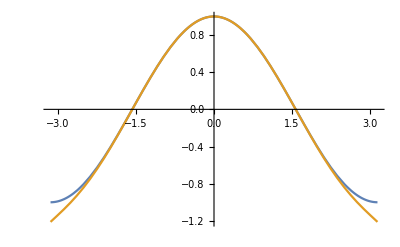

```mathematica
Plot[{f[x], P[x, 6]}, {x, -Pi, Pi}]
```

### INTEGRALES

```mathematica
Integrate[1/(x^7 + 3x^5 - 2x^3+1), {x, 3, 5}]
```

-RootSum[1-2 #1^3+3 #1^5+#1^7&,Log[3-#1]/(-6 #1^2+15 #1^4+7 #1^6)&]+RootSum[1-2 #1^3+3 #1^5+#1^7&,Log[5-#1]/(-6 #1^2+15 #1^4+7 #1^6)&]

EL MATEMATICA NO PUEDE SACAR LOS 0 POR LO QUE NO PUEDE RESOLVER ESTE TIPO DE INTREGRALES

```mathematica
f[x_] := Cos[x]
```

```mathematica
a = 0;
b = Pi / 2
recizq = f[a] (b- a);
recder = f[b] (b-a);
punt = f[(a+b)/2] (b-a);
trap = ((f[a] + f[b])/2) (b-a);
simp = (f[a] + 4f[((a+b)/2)]+f[b])/6 (b-a);

{∫_a^b f[x]ⅆx, recizq, recder, punt, trap, simp} // N
```

π/2

{1.,1.5708,0.,1.11072,0.785398,1.00228}

```mathematica
n = 20;
xx  = Table[a+i (b-a)/n, {i, 0, n}];
```

```mathematica
recizqC = (b-a) * 1/n∑_(i=1)^n f[xx[[i]]] // N
```

1.03876

```mathematica
recderC = (b-a) * (1/n) ∑_(i=2)^(n+1) f[xx[[i]]] // N
```

0.960216